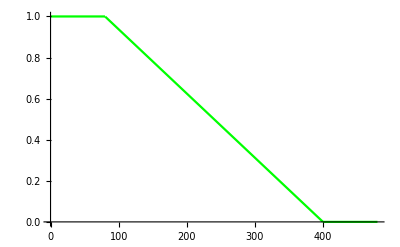

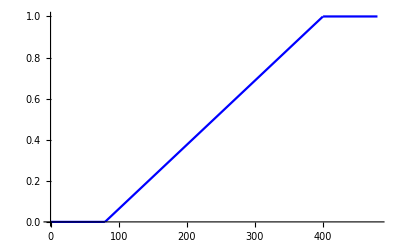

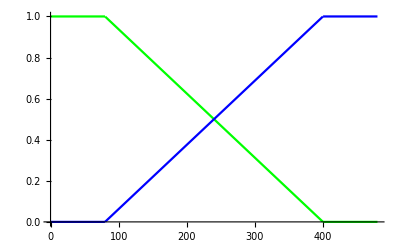

```mathematica
near=Plot[Piecewise[{{1,0<x<80},{-(1/320)*x+5/4,80<x<400},{0,400<x<480}}],{x,0,480},PlotStyle->Green]
far=Plot[Piecewise[{{0,0<x<80},{(1/320)*x-1/4,80<x<400},{1,400<x<480}}],{x,0,480},PlotStyle->Blue]
Show[near,far]
```

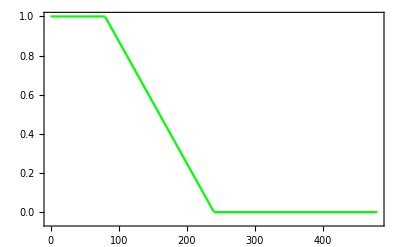

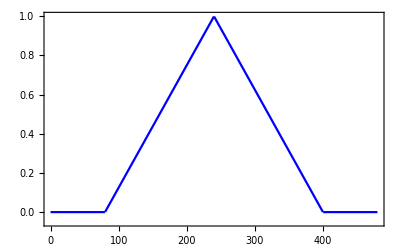

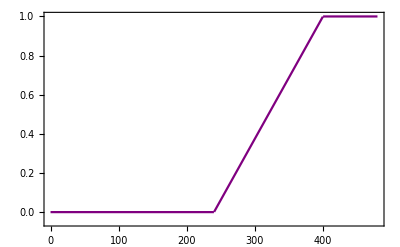

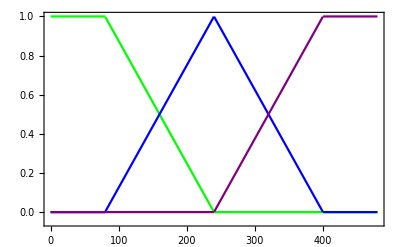

Piecewise::pairs: The first argument {{0,True},{-0.499939,False},{2.49994,False},{0,False,480}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {{0.,True},{-0.499939,False},{2.49994,False},{0.,False,480.}} of Piecewise is not a list of pairs.

Piecewise::pairs: The first argument {{0,True},{-0.438714,False},{2.43871,False},{0,False,480}} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise::pairs will be suppressed during this calculation.

-Graphics-

```mathematica
near=Plot[Piecewise[{{1,0≤x<80},{-(1/160)*x+3/2,80≤x<240},{0,240≤x≤480}}],{x,0,480},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Green]
middle=Plot[Piecewise[{{0,0≤x<80},{(1/160)*x-1/2,80≤x<240},{-(1/160)*x+5/2,240≤x<400},{0,400≤x≤480}}],{x,0,480},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Blue]
far=Plot[Piecewise[{{0,0≤x<240},{(1/160)*x-3/2,240≤x<400},{1,240≤x<480}}],{x,0,480},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Purple]
Show[near,middle,far,Frame->True,Axes->True,AxesOrigin->{0,-0.2}]
```

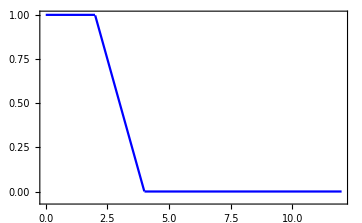

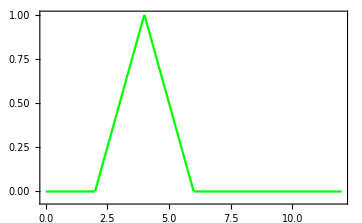

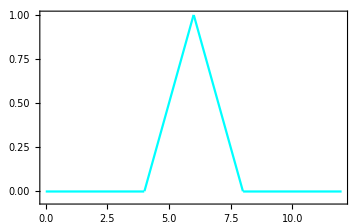

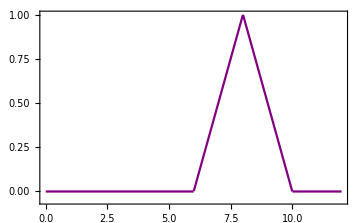

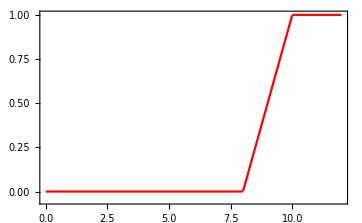

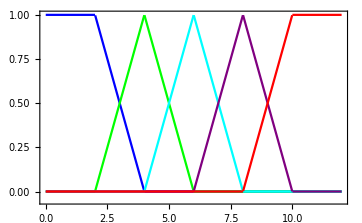

```mathematica
ss=Plot[Piecewise[{{1,0≤x<2},{-(1/2)*x+2,2≤x<4},{0,4≤x≤12}}],{x,0,12},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Blue]
s=Plot[Piecewise[{{0,0≤x<2},{(1/2)*x-1,2≤x<4},{-(1/2)*x+3,4≤x<6},{0,6≤x≤12}}],{x,0,12},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Green]
m=Plot[Piecewise[{{0,0≤x<4},{(1/2)*x-2,4≤x<6},{-(1/2)*x+4,6≤x<8},{0,8≤x≤12}}],{x,0,12},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Cyan]
f=Plot[Piecewise[{{0,0≤x<6},{(1/2)*x-3,6≤x<8},{-(1/2)*x+5,8≤x<10},{0,10≤x≤12}}],{x,0,12},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Purple]
ff=Plot[Piecewise[{{0,0≤x<8},{(1/2)*x-4,8≤x<10},{1,10≤x≤12}}],{x,0,12},Frame->True,Axes->True,AxesOrigin->{0,-0.05},PlotStyle->Red]
Show[ss,s,m,f,ff]
```